## Import data files and create interpolation objects

Form factors span the range q = 1 to 2000 keV and E = 1 eV to 2 keV. 
q is the momentum transfer [in keV] and E is the electron kinetic energy [in keV].
Data is optimised for q = 1 to 500 keV and E = 1 eV to 1 keV. 
Interpolation outside this range is not accurate.
Outgoing electron wave functions are Coulomb waves with Zeff values from ionisation energies

```mathematica
SetDirectory[NotebookDirectory[]];
LNe1sgrid=Import["Ne1s_CW_grid.dat"];
LNe2sgrid=Import["Ne2s_CW_grid.dat"];
LNe2pgrid=Import["Ne2p_CW_grid.dat"];
ResetDirectory[];

fNe1s=Interpolation[LNe1sgrid,InterpolationOrder->1]
fNe2s=Interpolation[LNe2sgrid,InterpolationOrder->1]
fNe2p=Interpolation[LNe2pgrid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

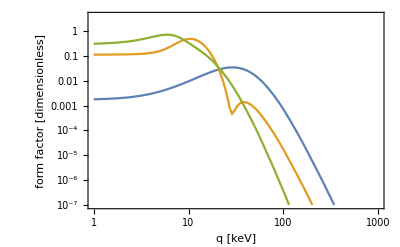

```mathematica
EtestkeV=0.025;

LogLogPlot[{fNe1s[q,EtestkeV],fNe2s[q,EtestkeV],fNe2p[q,EtestkeV]},{q,1,1000},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```